Singlet and triplet potentials from LeRoy code:

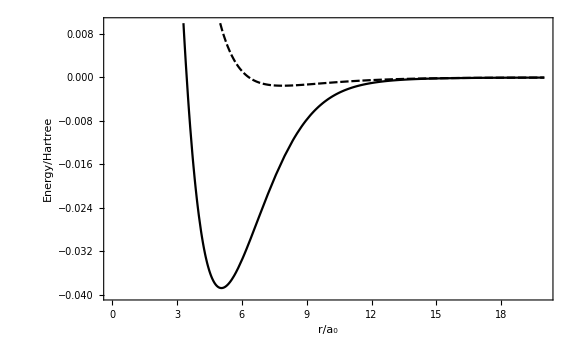

```mathematica
Singlet = Interpolation[Import["/Users/alysonlaskowski/LiScattering/fort.10"]];
Triplet = Interpolation[Import["/Users/alysonlaskowski/LiScattering/fort.30"]];
Plot[{Singlet[r],Triplet[r]},{r,1,20},Frame->True,PlotRange->{-0.040,0.010},ImageSize->Large,FrameLabel->{"r/a_0","Energy/Hartree"},LabelStyle->Large]
```

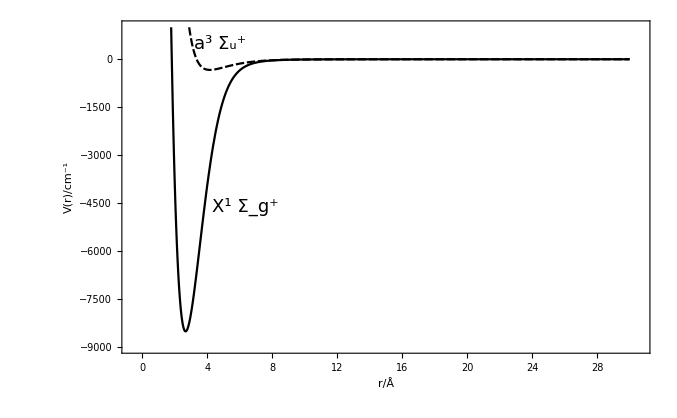

MLR singlet and triplet potentials with damping functions :

There are two shortcomings of MLR potentials (LeRoy et al. 2011):

1. The long-range behavior or MLR potentials is based on a sum of simple inverse-power terms and neglects the ‘damping’ of these terms due to the electron distribution overlap which occurs as atoms approach one another.

2. In the very short-range MLR potentials are excessively (unphysically so) steep.

i. Define well depths D_e, equilibrium internuclear distances r_e, reference distance r_ref, and coefficients in long-range interaction (energy in cm^-1 and length in Å)

```mathematica
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
t10 = 2.78683*10^9;
```

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/(0.529177210903);
```

Parameters with energy in Hartree and length in Bohr

```mathematica
sdeHB = sde*invcminHartree;
tdeHB = tde*invcminHartree;
sreHB =sre*AngstrominBohr;
treHB = tre*AngstrominBohr;
srefHB =sref*AngstrominBohr;
trefHB = tref*AngstrominBohr;
sc6HB = C6*invcminHartree*AngstrominBohr^-6;
sc8HB =C8*invcminHartree*AngstrominBohr^-8;
sc10HB =C10*invcminHartree*AngstrominBohr^-10;
tc6HB=tc6*invcminHartree*AngstrominBohr^-6;
tc8HB=tc8*invcminHartree*AngstrominBohr^-8;
tc10HB=t10*invcminHartree*AngstrominBohr^-10;
```

ii. Define parameters p and q used in radial variable y(r), ρ used in damping functions, and β coefficients

```mathematica
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
```

iii. Setup functions for β(r), y(r), and u_LR(r)

```mathematica
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
Clear[βinf]
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
β[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

```mathematica
βinf[tde,tre,DDS[tre,6,3.30,0.423,ρ1,-1],DDS[tre,8,3.30,0.423,ρ1,-1],DDS[tre,10,3.30,0.423,ρ1,-1],tc6,tc8,t10]
```

-0.509836

iv. Damping functions

1. Douketis damping coefficients from LeRoy and Dattani, Journal of Molecular Spectroscopy 268 (2011) 199-210

D_m^(DS(s))(r) = (1-e^(-((b^ds(s) (ρ r))/m+((c^ds(ρ r))^2)/m)))^(m+s)

2. Douketis damping coefficients from LeRoy et al., Molecular Physics 109 (2011) 435-446

D_m^(DS(s))(r) = (1-e^(-((b^ds(s) (ρ r))/m+((c^ds(ρ r))^2)/m^(1/2))))^(m+s)

3. Tang-Toennies damping coefficients from LeRoy et al., Molecular Physics 109 (2011) 435-446

D_m^(TT(s))= 1-e^(-b^tt(s)(ρ r))(∑^(m-1+s))_(k=0)((b^tt(s) (ρ r))^k)/(k!)

```mathematica
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DTT[r_,m_,btt_,ρ_,s_]:= 1-Exp[-btt ρ r]*Sum[(btt ρ r)^k/(k!),{k,0,m-1+s}];
```

v. MLR potential function

```mathematica
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
```

MLR potentials with no damping

```mathematica
sgmlr[r_]:= VMLR[r,sre,sde,β[r,sβcf1,βinf[sde,sre,1,1,1,C6,C8,C10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,C6,C8,C10]
```

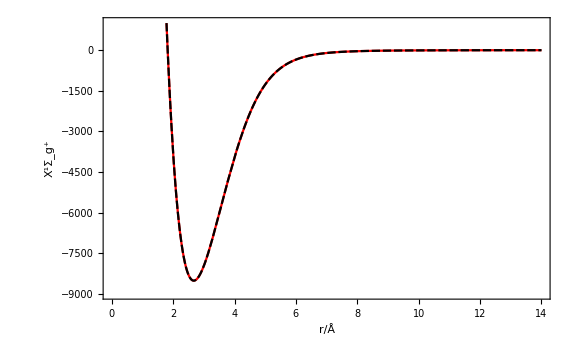

```mathematica
Plot[{sgmlr[r],Singlet[r]},{r,1.5,14},Frame->True,FrameLabel->{"r/Å","X^1Σ_g^+"},PlotStyle->{Red,Black},PlotRange->{-9000,1000},LabelStyle->Medium,ImageSize->Large]
```

```mathematica
tpmlr[r_]:= VMLR[r,tre,tde,β[r,tβcf,βinf[tde,tre,1,1,1,tc6,tc8,t10],y[tre,r,p],y[tref,r,p],y[tref,r,q]],y[tre,r,p],1,1,1,tc6,tc8,t10];
```

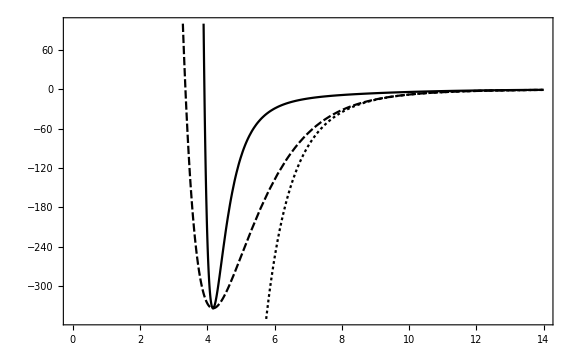

```mathematica
Plot[{tpmlr[r],Triplet[r],-ulr[r, 1,1,1,tc6,tc8,t10]},{r,1.5,14},Frame->True,LabelStyle->Medium,ImageSize->Large,PlotRange->{-350,100}]
```

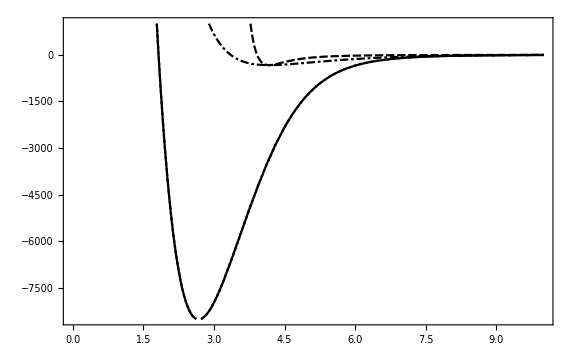

```mathematica
Plot[{sgmlr[r],tpmlr[r],Singlet[r],Triplet[r]},{r,1.0,10},Frame->True,ImageSize->Large,PlotRange->{-8500,1000}]
```

With Douketis (1) damping coefficients (for triplet)

```mathematica
tpdsmlr[r_]:=VMLR[r,tre,tde,β[r,tβcf,βinf[tde,tre,DDS[r,6,3.69,0.405,ρ1,-1/2],DDS[r,8,3.69,0.405,ρ1,-1/2],DDS[r,10,3.69,0.405,ρ1,-1/2],tc6,tc8,t10],y[tre,r,p],y[tref,r,p],y[tref,r,q]],y[tre,r,p],DDS[r,6,3.69,0.405,ρ1,-1/2],DDS[r,8,3.69,0.405,ρ1,-1/2],DDS[r,10,3.69,0.405,ρ1,-1/2],tc6,tc8,t10]
tpdsmlr2[r_]:=VMLR[r,tre,tde,β[r,tβcf,βinf[tde,tre,DDS[tre,6,3.30,0.423,ρ1,-1],DDS[tre,8,3.30,0.423,ρ1,-1],DDS[tre,10,3.30,0.423,ρ1,-1],tc6,tc8,t10],y[tre,r,p],y[tref,r,p],y[tref,r,q]],y[tre,r,p],DDS[r,6,3.30,0.423,ρ1,-1],DDS[r,8,3.30,0.423,ρ1,-1],DDS[r,10,3.30,0.423,ρ1,-1],tc6,tc8,t10]
```

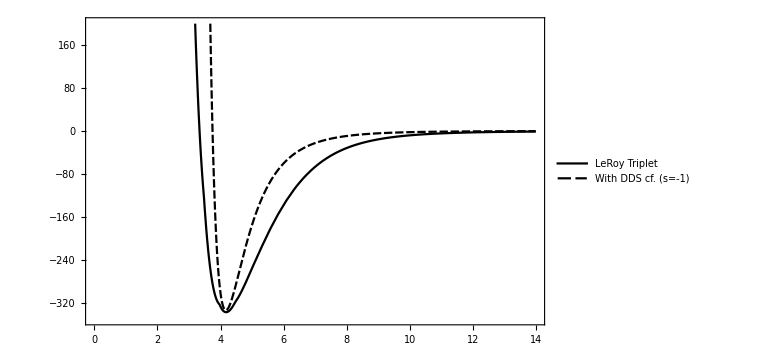

```mathematica
Plot[{Triplet[r],tpdsmlr2[r]},{r,1.5,14},Frame->True,PlotRange->{-350,200},LabelStyle->Medium,ImageSize->Large,PlotLegends->{"LeRoy Triplet","With DDS cf. (s=-1)"}]
```

With Tang-Toennies damping coefficients (for triplet)

```mathematica
tpdttmlr[r_]:=VMLR[r,tre,tde,β[r,tβcf,βinf[tde,tre,DTT[r,6,2.78,ρ1,0],DTT[r,8,2.78,ρ1,0],DTT[r,10,2.78,ρ1,0],tc6,tc8,t10],y[tre,r,p],y[tref,r,p],y[tref,r,q]],y[tre,r,p],DTT[r,6,2.78,ρ1,0],DTT[r,8,2.78,ρ1,0],DTT[r,10,2.78,ρ1,0],tc6,tc8,t10]
```

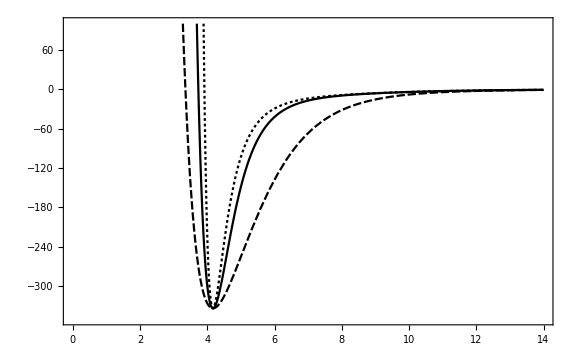

```mathematica
Plot[{tpdttmlr[r],Triplet[r],tpmlr[r]},{r,1.5,14},Frame->True,PlotRange->{-350,100},LabelStyle->Medium,ImageSize->Large]
```

Define electronic spin, nuclear spin, hyperfine constant, gyromagnetic ratios for electron and nucleus, nuclear and Bohr magnetons:

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
```

Hyperfine constant in THz:

```mathematica
Li7A = 401.75204335 * 10^-6;
```

Hyperfine constant in cm^-1:

```mathematica
Li7Acm = (Li7A *6.626*10^-34*10^12)/(1.986*10^-23)
```

0.0134039

Nuclear and Bohr Magnetons in units THz/G:

```mathematica
μb = (9.27*10^-24)/(6.626*10^-34)*10^-12*(1/10^4)
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4)
```

1.39903×10^-6

7.62267×10^-10

Nuclear and Bohr Magnetons in cm^-1/G:

```mathematica
μbcm = (μb *6.626*10^-34*10^12)/(1.986*10^-23)
μncm = (μn *6.626*10^-34*10^12)/(1.986*10^-23)
```

0.0000466767

2.54319×10^-8

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

```mathematica
mF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
```

Unsymmetrized Basis

```mathematica
mF2unsym =Select[f1m1f2m2basis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

```mathematica
mF2sym = Table[MatrixForm[mF2unsym[[i]]]+MatrixForm[Flatten[{mF2unsym[[i,3;;4]],mF2unsym[[i,1;;2]]}]],{i,1,Length[mF2unsym]}]
```

{(1
0
2
2)+(2
2
1
0),2 (1
1
1
1),(1
1
2
1)+(2
1
1
1),(2
0
2
2)+(2
2
2
0),(1
1
2
1)+(2
1
1
1),2 (2
1
2
1),(1
0
2
2)+(2
2
1
0),(2
0
2
2)+(2
2
2
0)}

Symmetrized Basis

```mathematica
DeleteDuplicates[mF2sym]
```

{(1
0
2
2)+(2
2
1
0),2 (1
1
1
1),(1
1
2
1)+(2
1
1
1),(2
0
2
2)+(2
2
2
0),2 (2
1
2
1)}

Singlet and triplet projection operators in hyperfine basis (given in Appendix B of McAlexander Thesis):

1. First expand the hyperfine basis into a linear combination of the molecular basis (i.e. the basis with S = s_1+s_2, I = i_1+i_2, m_S, and m_I as “good” quantum numbers) which are eigenstates of the triplet and singlet operators:

|f_1 m_f_1 f_2 m_f_2⟩ = ∑⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ |S m_s I m_I⟩

where ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ is the Clebsch-Gordan coefficient and is found by the following procedure:

1.a) De-couple |f_1 m_f_1 f_2 m_f_2⟩ basis into the atomic basis (i.e. the basis with m_s_1, m_s_2, m_i_1, and m_i_2 as “good” quantum numbers) through the expression:

|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2)|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩

1.b) Re-couple the atomic basis |s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩ to the molecular basis |S m_s I m_I⟩:

|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩=∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.c) Use the expressions of (1.a) and (1.b) to express the hyperfine basis  |f_1 m_f_1 f_2 m_f_2⟩ in terms of the molecular basis |S m_s I m_I⟩ :

|f_1 m_f_1 f_2 m_f_2⟩ =(-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.d) Take the inner product with |S' m_s'I 'm_I'⟩ to find an expression for ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I) ⟨S' m_s'I 'm_I'|S m_s I m_I⟩

= (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (-1)^(-m_S'-m_I')√((2S'+1)(2I'+1))(s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩= ((-1)^(2 i_2-2 s_1-m_1-m_2))^(-m_S'-m_I')√((2 f_1+1)(2 f_2+1)(2S'+1)(2I'+1))∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

2. Using Eq. 23 with the Clebsch-Gordan coefficients given by Eq. 29, determine the matrix elements ⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ for the projection operators in the hyperfine basis:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| P_(0 or 1)|S m_s I m_I⟩

The projection operator P_(0 or 1) acts on the state |S m_s I m_I⟩ like a delta function where P_0=δ_(S,0) and P_1=δ_(S,1), and thus the matrix elements are:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| δ_(S, 0 or 1)|S m_s I m_I⟩

= ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0 or 1)

Note that the above expression only holds for an unsymmetrized basis set. For a symmetrized basis set with states {αβ=(αβ±(-1)^l βα)/(√(2(1+δ_αβ))) the elements of the projection operator P_(0 or 1) are:

{α'β'}P_(0 or 1){αβ}={α'β'}P_(0 or 1)(αβ±(-1)^l βα)/(√(2(1+δ_αβ)))

=1/(√(2(1+δ_αβ)))({α'β'}P_(0 or 1)αβ±(-1)^l{α'β'}P_(0 or 1)βα)

=1/(√(2(1+δ_αβ)))1/(√(2(1+δ_α'β')))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα).

Can this expression be simplified further? What are the relationships between α'β' P_(0 or 1)αβ, β'α' P_(0 or 1)βα, β'α' P_(0 or 1)αβ and α'β' P_(0 or 1)βα?

Define the exchange operator, 𝒫, which interchanges two particles:

𝒫αβ=βα

where α corresponds to particle 1 and β to particle 2 in αβ and vice versa in βα. Moreover, if we apply 𝒫 twice to αβ, we should find that the system returns to its original state:

𝒫^2 αβ=αβ.

Therefore, 𝒫^2=1 and it follows that the eigenvalues of 𝒫 are ±1. If the particles are identical, the Hamiltonian must treat them the same, and thus, 𝒫 and H are compatible observables: [𝒫,H]=0 and we can find a complete set of functions that are simultaneous eigenstates of both. These solutions can be either symmetric (eigenvalue +1; for bosons) or antisymmetric (eigenvalue -1; for fermions) under exchange:

𝒫{αβ}=±αβ=βα→ αβ=±βα.

Using the above relationship, we can rewrite the matrix element β'α' P_(0 or 1)βα as

α'β' P_(0 or 1)αβ=±β'α' P_(0 or 1)±βα=β'α' P_(0 or 1)βα

and simplify our expression for {α'β'}P_(0 or 1){αβ} to

{α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(2α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα).

Similarly, the matrix element β'α' P_(0 or 1)αβ can be rewritten as

β'α' P_(0 or 1)αβ=±α'β' P_(0 or 1)±βα=α'β' P_(0 or 1)βα.

This simplifies {α'β'}P_(0 or 1){αβ} further to

{α'β'}P_(0 or 1){αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ).

Construct projection matrices in hyperfine basis:

Function to calculate coefficients ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];

ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];
```

Singlet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0) (for unsymmetrized basis, i.e., used for distinguishable particles):

```mathematica
SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];
```

For symmetrized basis; p=0 corresponds to bosons, p=1 to fermions

I. Using  {α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

```mathematica
SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi7=FullSimplify[SingletProjectionSym[0,0]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1/2,-1/2},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
N[MatrixForm[SProjSymLi7]]
```

(0.1875 | 0.153093 | -0.216506 | 0.216506 | -0.1875
0.153093 | 0.125 | -0.176777 | 0.176777 | -0.153093
-0.216506 | -0.176777 | 0.25 | -0.25 | 0.216506
0.216506 | 0.176777 | -0.25 | 0.25 | -0.216506
-0.1875 | -0.153093 | 0.216506 | -0.216506 | 0.1875)

```mathematica
MatrixForm[SProjSymLi7.SProjSymLi7]
```

(3/16 | (√(3/2))/8 | -(√3)/8 | (√3)/8 | -3/16
(√(3/2))/8 | 1/8 | -1/(4 √2) | 1/(4 √2) | -(√(3/2))/8
-(√3)/8 | -1/(4 √2) | 1/4 | -1/4 | (√3)/8
(√3)/8 | 1/(4 √2) | -1/4 | 1/4 | -(√3)/8
-3/16 | -(√(3/2))/8 | (√3)/8 | -(√3)/8 | 3/16)

II. Using {α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(2α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

```mathematica
SingletProjectionSym2[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(2 ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi72=FullSimplify[SingletProjectionSym2[0,0]];
```

```mathematica
MatrixForm[SProjSymLi7-SProjSymLi72]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

Expression (I) and (II) for the singlet projection operator are equivalent.

III. Using {α'β'}P_(0 or 1){αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ)

```mathematica
SingletProjectionSym3[p_,l_]:= Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi73=FullSimplify[SingletProjectionSym3[0,0]];
```

```mathematica
MatrixForm[SProjSymLi73-SProjSymLi7]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

Expression (III) for the singlet projection operator is equivalent to (I) and (II)

Triplet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 1) (for unsymmetrized basis):

```mathematica
TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];
```

For symmetrized basis:

```mathematica
TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]),{j,1,5},{jp,1,5}]
```

```mathematica
TProjSymLi7=FullSimplify[TripletProjectSym[0,0]];
```

```mathematica
N[MatrixForm[TProjSymLi7]]
```

(0.8125 | -0.153093 | 0.216506 | -0.216506 | 0.1875
-0.153093 | 0.875 | 0.176777 | -0.176777 | 0.153093
0.216506 | 0.176777 | 0.75 | 0.25 | -0.216506
-0.216506 | -0.176777 | 0.25 | 0.75 | 0.216506
0.1875 | 0.153093 | -0.216506 | 0.216506 | 0.8125)

Combined Zeeman and Hyperfine Interactions (From McAlexander Appendix E)

McAlexander Eq. E.2

(s i)f'm' H^HZ(s i)f m=A^HF/2[f(f+1)-s(s+1)-i(i+1)]δ_ff' δ_mm'+g_s μ_B B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_s(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'+g_i μ_N B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_i(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbcm B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μncm B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7[B_]:=FullSimplify[HZsym[0,0,B]];
```

```mathematica
MatrixForm[HZsymLi7[B]]
```

(-0.0335097-0.0000465387 B | 0.0000571333 B | 0. | 0. | 0
0.0000571333 B | -0.00670194+1.10421×10^-7 B | 0. | 0. | 0.0000571333 B
0. | 0. | -0.00670194+0.0000467596 B | 0.+0.0000466491 B | 0.
0. | 0. | 0.+0.0000466491 B | 0.0201058+0.0000467596 B | 0.
0 | 0.0000571333 B | 0. | 0. | 0.0201058+0.0000467596 B)

```mathematica
Htest[r_,B_]:= HZsymLi7[B]+TProjSymLi7*Triplet[r]+SProjSymLi7*Singlet[r];
```

```mathematica
SingletMatrix2[r_]:= HZsymLi7[0]+SProjSymLi7 Singlet[r];
TripletMatrix2[r_]:= HZsymLi7[0]+TProjSymLi7 Triplet[r];
```

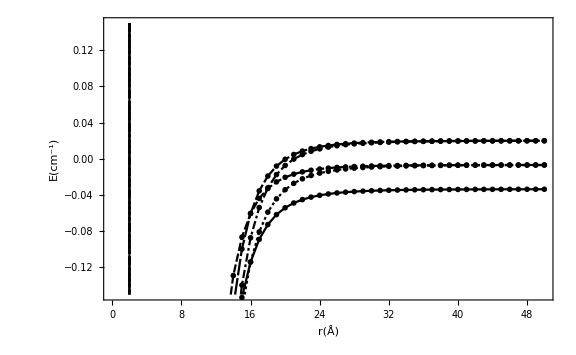

```mathematica
ListLinePlot[{Table[{j, SingletMatrix2[j][[1, 1]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[2, 2]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[3, 3]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[4, 4]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[5, 5]]}, {j, 1, 50}]},ImageSize->Large,Frame->True,FrameLabel->{"r(Å)","E(cm^-1)"},LabelStyle->Medium,PlotRange->{-0.15,0.15}]
```

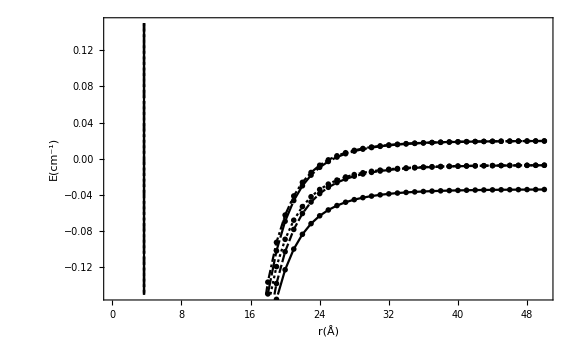

```mathematica
ListLinePlot[{Table[{j, TripletMatrix2[j][[1, 1]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[2, 2]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[3, 3]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[4, 4]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[5, 5]]}, {j, 1, 50}]},ImageSize->Large,Frame->True,FrameLabel->{"r(Å)","E(cm^-1)"},LabelStyle->Medium,PlotRange->{-0.15,0.15}]
```

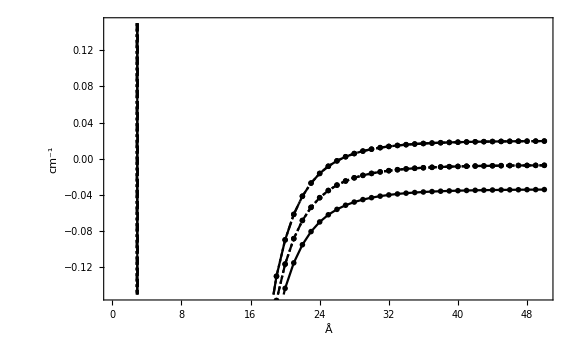

```mathematica
ListLinePlot[{Table[{j, Htest[j, 0][[1, 1]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[2, 2]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[3, 3]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[4, 4]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[5, 5]]}, {j, 1, 50}]},Frame->True,ImageSize->Large,FrameLabel->{"Å","cm^-1"},PlotRange->{-0.15,0.15},LabelStyle->Large]
```

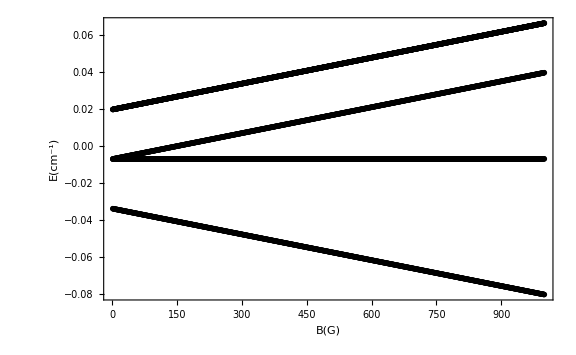

```mathematica
ListLinePlot[{Table[{j, Htest[50, j][[1, 1]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[2, 2]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[3, 3]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[4, 4]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[5, 5]]}, {j, 1, 1000}]},  ImageSize-> Large, Frame ->True, FrameLabel ->{"B(G)", "E(cm^-1)" }, LabelStyle ->Medium]
```

Single Channel Calculation Using {2222} state of ^7 Li +^7 Li

{2222} is a pure triplet with m_F=m_1+m_2=m_S+m_I=4. Moreover, it is the only symmetrized state with m_F=4, and thus, it is not coupled to any other {f_1 m_1 f_2 m_2}. The Hamiltonian for this state is given by

H = -ℏ^2/(2μ) d^2/(d r^2)+ H_1^HZ+H_2^HZ+V_1(r)+(l(l+1)ℏ^2)/(2 μr^2)

=-ℏ^2/(2μ) d^2/(d r^2)+ 2 H_1^HZ+V_1(r)+(l(l+1)ℏ^2)/(2 μr^2)

where H_1^HZ=H_2^HZ because f_1=f_2 and m_1=m_2.

```mathematica
2*HZ[2,2,2,2,Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]
```

2 (0.0100529+0.0000467596 B)

```mathematica
ProjectionMatrixElement[2,2,2,2,2,2,2,2,Li7s,Li7i,Li7s,Li7i,0]
```

0

```mathematica
ProjectionMatrixElement[2,2,2,2,2,2,2,2,Li7s,Li7i,Li7s,Li7i,1]
```

1

The singlet projection operator should be zero and the triplet projection operator should be one if {2222} is a pure triplet.

```mathematica
HLi7mF4[r_,l_,B_]:= 2*HZ[2,2,2,2,Li7s,Li7i,Li7gs,Li7gi,Li7Acm,B]+Triplet[r]+(l(l+1))/r^2;
```

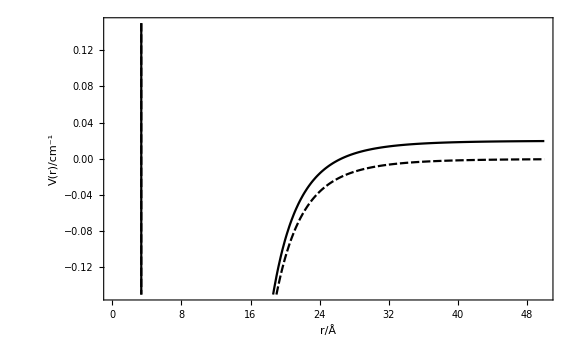

```mathematica
Plot[{HLi7mF4[r,0,0],Triplet[r]},{r,1.0,50},Frame->True,FrameLabel->{"r/Å","V(r)/cm^-1"},ImageSize->Large,LabelStyle->Medium,PlotRange->{-0.15,0.15}]
```

```mathematica
CalcCotanDelta[v0_,r0_,ksqr_,rmax_,rmin_]:=
Module[{vlocal,CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;
vlocal=v0;
k=√ksqr;
sol=NDSolve[{-u''[r]+vlocal u[r]==ksqr u[r],u[r0]==0,u'[r0]==1},u,{r,rmin,rmax},MaxSteps->∞];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERE[v0_,r0_,rmax_,rmin_,ksqrMin_,ksqrMax_]:=
Module[{vlocal,EREData,ascat,reff,A,B,fitpars,dE},
dE=(ksqrMax-ksqrMin)/10;
vlocal=v0;
EREData=Table[{ksqr,√ksqr CalcCotanDelta[vlocal,r0,ksqr,rmax,rmin]},{ksqr,ksqrMin,ksqrMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff}]
]
```

```mathematica
Clear[ksqr,rmin,rmax]
```

```mathematica
rmin = 1.0;
rmax = 500;
ksqrMin = 0.00001;
ksqrMax =0.001 ;
r0 = 1.0;
```

```mathematica
{ascat,reff}=CalcERE[Triplet[r],r0,rmax,rmin,ksqrMin,ksqrMax]
```

{1.29813,37.7427}

```mathematica
sol = NDSolve[{-u''[r]+ Triplet[r]*u[r]==ksqrMax u[r],u[r0]==0,u'[r0]==1},u,{r,rmin,rmax}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot[u[r]/.sol,{r,r0,10},Frame->True,ImageSize->Large,GridLines->Automatic]
```